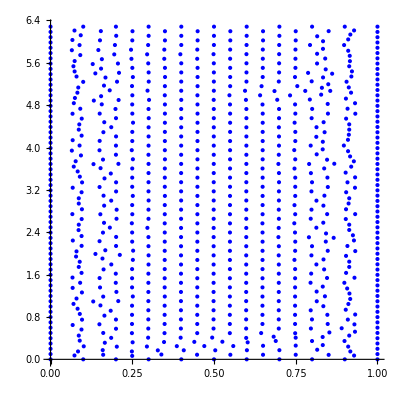

827

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/2d/square_no_circle/solution/vertices.csv"]
tabve=Table[{tabve[[i,1]],tabve[[i,2]]},{i,2,Length[tabve]}]
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
Length[tabve]
```

```mathematica
(*write X from ODE to csv file*)
```

```mathematica
tabψ=Table[{
ψ[s]/.sol/.{s->tabve[[i,1]]},
tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabψ,{"f:",":0",":1",":2"}]
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/solution_ode/psi_ode.csv",tabψ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/solution_ode/psi_ode.csv

```mathematica
(*write μ from ODE to csv file*)
```

```mathematica
tabμ=Table[{
H[s]/.sol/.{s->tabve[[i,1]]},
tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabμ,{"f:",":0",":1",":2"}]
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/solution_ode/mu_ode.csv",tabμ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/solution_ode/mu_ode.csv

```mathematica
(*write omega from ODE to csv file*)
```

```mathematica
tabω=Table[Flatten[{
e[1][{s,θ}]/.sol/.{s->tabve[[i,1]],θ->tabve[[i,2]]},
e[2][{s,θ}]/.sol/.{s->tabve[[i,1]],θ->tabve[[i,2]]},
tabve[[i,1]],tabve[[i,2]],0}],{i,1,Length[tabve]}];
PrependTo[tabω,{"f:0","f:1","f:2","f:3","f:4","f:5",":0",":1",":2"}]
(*tabω=Table[Flatten[{
{Cos[2π tabve[[i,1]]],Cos[4π tabve[[i,1]]],Cos[8π tabve[[i,1]]]},
{Cos[tabve[[i,2]]],Cos[2 tabve[[i,2]]+2π tabve[[i,1]]],Cos[4tabve[[i,2]]]},
tabve[[i,1]],tabve[[i,2]],0}],{i,1,Length[tabve]}];
PrependTo[tabω,{"f:0","f:1","f:2","f:3","f:4","f:5",":0",":1",":2"}]*)
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/solution_ode/omega_ode.csv",tabω]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/solution_ode/omega_ode.csv